```mathematica
(*it somewhat improving accuracy by picking another sample data ,idk why*)
(*set directory for importing file*)
SetDirectory[NotebookDirectory[]];
myImport=Import["weather.xlsx",{"Data",1}] [[2;;]];
```

```mathematica
(*transform into a list*)
```

```mathematica
myData=Thread[myImport[[1;;,1;;-2]]->myImport[[1;;,-1]]];
```

```mathematica
(*pick 80% of sample data from myData and 20% for evaluating*)
```

```mathematica
sampleSize=IntegerPart[Length@myData*0.8];
myDataTrain=RandomSample[myData,sampleSize];
myDataTest=Complement[myData,myDataTrain];
```

```mathematica
(*auto train*)
```

```mathematica
myClassify=Classify[myDataTrain]
```

ClassifierFunction[…]

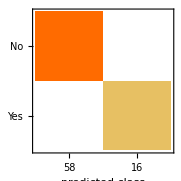
Classifier Measurements
Classifier method | DecisionTree
Number of test examples | 74
Accuracy | (100.00000000000000022) %
Accuracy baseline | (78.5.) %
Geometric mean of probabilities | 0.998 ± 0.00025
Mean cross entropy | 0.00176 ± 0.00025
Single evaluation time | 8.71 ms/example
Batch evaluation speed | 2.22 examples/ms
-Graphics- |

ClassifierMeasurementsObject::elmntav: "ResidualPlot" is not an available property.

{Classifier Measurements
Classifier method | DecisionTree
Number of test examples | 74
Accuracy | (100.00000000000000022) %
Accuracy baseline | (78.5.) %
Geometric mean of probabilities | 0.998 ± 0.00025
Mean cross entropy | 0.00176 ± 0.00025
Single evaluation time | 8.71 ms/example
Batch evaluation speed | 2.22 examples/ms
-Graphics- | [ResidualPlot]}

```mathematica
(*accuracy test*)
myAccuracy=ClassifierMeasurements[myClassify,myDataTest];
myAccuracy["Report"]
myAccuracy/@{"ResidualPlot"}
```

```mathematica
(*save model *)
SetDirectory[NotebookDirectory[]];
DumpSave["classify_weather.mx",myClassify];
```

```mathematica
Get["classify_weather.mx",myClassify];
importProductionXLSX=SystemDialogInput["FileOpen",{NotebookDirectory[]<>"data\\",{"Data files"->{"*.xlsx"}}}];
BatchSpecimens=Import[importProductionXLSX,{"Data",1}] [[2;;]];
pResult=myClassify[BatchSpecimens]
```

ClassifierFunction::mlbftlgth2: Example {8.,24.3,0.,3.4,6.3,NW,30.,SW,NW,6.,«12»} should have 21 features instead of 22.

ClassifierFunction[…][{{8.,24.3,0.,3.4,6.3,NW,30.,SW,NW,6.,20.,68.,29.,1019.7,1015.,7.,7.,14.4,23.6,No,3.6,Yes},{14.,26.9,3.6,4.4,9.7,ENE,39.,E,W,4.,17.,80.,36.,1012.4,1008.4,5.,3.,17.5,25.7,Yes,3.6,Yes},{13.7,23.4,3.6,5.8,3.3,NW,85.,N,NNE,6.,6.,82.,69.,1009.5,1007.2,8.,7.,15.4,20.2,Yes,39.8,Yes},{13.3,15.5,39.8,7.2,9.1,NW,54.,WNW,W,30.,24.,62.,56.,1005.5,1007.,2.,7.,13.5,14.1,Yes,2.8,Yes},{7.6,16.1,2.8,5.6,10.6,SSE,50.,SSE,ESE,20.,28.,68.,49.,1018.3,1018.5,7.,7.,11.1,15.4,Yes,0.,No},{6.2,16.9,0.,5.8,8.2,SE,44.,SE,E,20.,24.,70.,57.,1023.8,1021.7,7.,5.,10.9,14.8,No,0.2,No},{6.1,18.2,0.2,4.2,8.4,SE,43.,SE,ESE,19.,26.,63.,47.,1024.6,1022.2,4.,6.,12.4,17.3,No,0.,No},{8.3,17.,0.,5.6,4.6,E,41.,SE,E,11.,24.,65.,57.,1026.2,1024.2,6.,7.,12.1,15.5,No,0.,No},{8.8,19.5,0.,4.,4.1,S,48.,E,ENE,19.,17.,70.,48.,1026.1,1022.7,7.,7.,14.1,18.9,No,16.2,Yes},{8.4,22.8,16.2,5.4,7.7,E,31.,S,ESE,7.,6.,82.,32.,1024.1,1020.7,7.,1.,13.3,21.7,Yes,0.,No},{9.1,25.2,0.,4.2,11.9,N,30.,SE,NW,6.,9.,74.,34.,1024.4,1021.1,1.,2.,14.6,24.,No,0.2,No},{8.5,27.3,0.2,7.2,12.5,E,41.,E,NW,2.,15.,54.,35.,1023.8,1019.9,0.,3.,16.8,26.,No,0.,No},{10.1,27.9,0.,7.2,13.,WNW,30.,S,NW,6.,7.,62.,29.,1022.,1017.1,0.,1.,17.,27.1,No,0.,No},{12.1,30.9,0.,6.2,12.4,NW,44.,WNW,W,7.,20.,67.,20.,1017.3,1013.1,1.,4.,19.7,30.7,No,0.,No},{10.1,31.2,0.,8.8,13.1,NW,41.,S,W,6.,20.,45.,16.,1018.2,1013.7,0.,1.,18.7,30.4,No,0.,No},{12.4,32.1,0.,8.4,11.1,E,46.,SE,WSW,7.,9.,70.,22.,1017.9,1012.8,0.,3.,19.1,30.7,No,0.,No},{13.8,31.2,0.,7.2,8.4,ESE,44.,WSW,W,6.,19.,72.,23.,1014.4,1009.8,7.,6.,20.2,29.8,No,1.2,Yes},{11.7,30.,1.2,7.2,10.1,S,52.,SW,NE,6.,11.,59.,26.,1016.4,1013.,1.,5.,20.1,28.6,Yes,0.6,No},{12.4,32.3,0.6,7.4,13.,E,39.,NNE,W,4.,17.,60.,25.,1017.1,1013.3,1.,3.,20.2,31.2,No,0.,No},{15.6,33.4,0.,8.,10.4,NE,33.,NNW,NNW,2.,13.,61.,27.,1018.5,1013.7,0.,1.,22.8,32.,No,0.,No},{15.3,33.4,0.,8.8,9.5,WNW,59.,N,NW,2.,31.,60.,26.,1012.4,1006.5,1.,5.,22.2,32.8,No,0.4,No},{16.4,19.4,0.4,9.2,0.,E,26.,ENE,E,6.,11.,88.,72.,1010.7,1008.9,8.,8.,16.5,18.3,No,25.8,Yes},{12.8,18.5,25.8,2.8,0.6,ESE,28.,S,SE,13.,13.,91.,79.,1014.,1014.9,8.,8.,14.,16.8,Yes,0.4,No},{12.,24.3,0.4,1.2,7.5,NNE,26.,WSW,NE,6.,9.,74.,57.,1020.7,1019.2,7.,5.,17.8,22.8,No,0.,No},{15.4,28.4,0.,4.4,8.1,ENE,33.,SSE,NE,9.,15.,85.,31.,1022.4,1018.6,8.,2.,16.8,27.3,No,0.,No},{15.6,26.9,0.,6.8,8.9,E,41.,E,E,6.,22.,65.,48.,1019.7,1016.5,2.,4.,19.8,25.1,No,0.2,No},{13.3,22.2,0.2,6.6,2.3,ENE,39.,E,E,20.,17.,70.,55.,1021.,1018.6,7.,7.,16.5,21.2,No,0.,No},{12.9,28.,0.,4.4,10.7,S,52.,S,NNE,6.,11.,61.,31.,1019.2,1014.8,5.,7.,18.8,26.7,No,0.,No},{15.1,24.3,0.,7.,0.4,SE,39.,SE,SE,7.,17.,69.,80.,1019.,1017.1,7.,7.,18.9,19.7,No,0.4,No},{13.6,24.1,0.4,2.6,0.5,NNW,30.,SSW,S,6.,6.,83.,49.,1017.2,1013.3,8.,7.,17.3,23.2,No,22.6,Yes},{15.1,20.4,22.6,2.4,0.2,SSE,41.,E,S,6.,20.,82.,90.,1015.,1014.1,8.,8.,17.,16.3,Yes,4.2,Yes},{11.6,26.3,4.2,1.6,12.,NNE,41.,E,SW,6.,9.,66.,46.,1013.9,1009.5,2.,2.,16.7,25.2,Yes,0.2,No},{16.6,24.2,0.2,6.6,4.7,NW,50.,WNW,NW,13.,35.,72.,60.,1007.9,1004.6,7.,7.,20.5,19.9,No,6.6,Yes},{13.3,26.5,6.6,3.8,11.8,NW,50.,NW,WNW,20.,26.,74.,40.,1007.3,1006.3,5.,2.,18.8,25.1,Yes,0.,No},{14.5,21.8,0.,8.4,9.8,ENE,43.,ESE,E,11.,30.,69.,63.,1015.,1015.3,7.,1.,18.6,20.5,No,0.,No},{16.3,26.8,0.,6.,6.3,ENE,39.,ESE,ESE,13.,9.,78.,54.,1018.8,1016.1,8.,7.,18.6,24.5,No,0.,No},{17.2,25.8,0.,4.2,8.8,SW,41.,NW,N,6.,6.,70.,74.,1014.5,1011.5,6.,7.,21.5,22.6,No,4.,Yes},{16.5,28.2,4.,4.2,8.8,NE,39.,E,N,7.,13.,76.,42.,1014.8,1011.4,8.,1.,18.,26.3,Yes,0.,No},{15.,29.4,0.,6.6,11.1,NW,43.,N,W,9.,24.,78.,24.,1010.8,1008.5,7.,7.,20.6,28.6,No,0.,No},{14.9,24.8,0.,10.4,10.,NNW,35.,NNE,WNW,11.,6.,58.,37.,1011.7,1010.4,7.,7.,19.3,22.9,No,0.6,No},{11.8,18.5,0.6,4.8,2.3,ENE,35.,ESE,E,9.,15.,60.,63.,1018.,1017.4,8.,6.,13.8,16.4,No,0.,No},{11.7,21.5,0.,4.2,7.3,ENE,41.,ESE,E,15.,24.,66.,51.,1021.1,1019.6,7.,5.,15.7,19.4,No,0.,No},{9.6,20.3,0.,5.,3.6,SE,39.,ESE,E,22.,20.,70.,49.,1021.9,1019.3,7.,7.,15.8,19.2,No,0.,No},{8.9,27.1,0.,4.4,12.7,E,35.,NNW,N,6.,11.,63.,37.,1018.1,1012.5,1.,2.,15.8,25.,No,0.,No},{10.1,29.9,0.,6.8,8.8,E,41.,SE,WNW,2.,13.,63.,36.,1012.6,1010.2,1.,8.,17.4,29.1,No,5.4,Yes},{15.5,21.1,5.4,6.4,0.9,S,31.,SSE,NE,6.,7.,93.,86.,1010.1,1008.6,8.,8.,16.6,20.,Yes,1.4,Yes},{10.8,21.7,1.4,2.8,10.6,ESE,48.,SSE,ESE,13.,20.,59.,40.,1017.6,1016.8,1.,4.,15.3,20.8,Yes,0.,No},{7.5,20.9,0.,6.6,8.7,ENE,39.,SE,E,13.,20.,61.,43.,1020.6,1018.3,6.,7.,15.3,19.8,No,0.,No},{12.8,21.,0.,6.4,0.8,NE,22.,NE,ENE,7.,6.,72.,54.,1018.,1015.6,8.,8.,16.1,20.,No,3.4,Yes},{12.6,23.1,3.4,1.6,2.3,NNW,30.,N,NW,4.,13.,97.,74.,1015.8,1014.1,8.,7.,15.3,20.4,Yes,6.4,Yes},{14.8,29.5,6.4,1.8,8.1,N,41.,NW,NW,6.,22.,81.,48.,1012.9,1008.3,2.,7.,21.,28.2,Yes,11.,Yes},{19.9,22.,11.,4.4,5.9,NNW,76.,N,WNW,41.,30.,92.,62.,996.5,996.8,8.,3.,20.6,19.6,Yes,17.4,Yes},{9.2,20.4,17.4,7.8,10.2,ENE,39.,N,N,9.,20.,59.,49.,1009.5,1009.1,1.,7.,14.9,18.8,Yes,0.,No},{12.4,24.4,0.,6.2,12.1,NW,44.,NNW,WNW,7.,13.,69.,43.,1012.8,1009.7,6.,4.,15.,22.5,No,3.4,Yes},{11.3,21.7,3.4,8.2,5.6,E,41.,SE,NE,11.,11.,67.,52.,1020.4,1019.1,8.,3.,12.4,21.,Yes,0.,No},{9.8,26.3,0.,5.2,13.,NNW,41.,W,NNW,6.,19.,63.,35.,1023.2,1018.,1.,1.,15.3,23.9,No,0.,No},{14.3,26.7,0.,7.2,7.1,NNW,65.,N,NNW,7.,48.,68.,64.,1017.3,1014.3,7.,7.,19.8,19.,No,14.4,Yes},{15.1,28.3,14.4,8.8,13.2,NNW,28.,NNW,NW,6.,13.,73.,44.,1016.8,1013.4,1.,5.,18.3,27.4,Yes,0.,No},{14.4,31.6,0.,6.6,13.6,NNW,30.,NW,N,6.,7.,65.,30.,1017.1,1014.2,0.,2.,21.5,30.3,No,0.,No},{15.4,35.,0.,9.6,13.,E,39.,SSW,ESE,6.,22.,55.,18.,1017.4,1015.,1.,1.,23.4,34.3,No,0.,No},{13.8,33.5,0.,11.4,13.6,NE,31.,SSE,NE,7.,9.,44.,20.,1019.2,1015.6,0.,1.,21.9,32.2,No,0.,No},{13.6,34.2,0.,8.8,12.8,NNE,35.,ESE,W,2.,11.,50.,20.,1015.8,1011.6,7.,6.,21.9,31.8,No,0.,No},{14.3,35.,0.,7.6,10.5,ESE,41.,ESE,WSW,2.,9.,43.,14.,1012.6,1008.7,0.,1.,23.,33.6,No,0.,No},{15.9,23.4,0.,12.6,2.2,ESE,50.,ESE,ESE,20.,24.,69.,55.,1016.8,1016.3,8.,7.,19.2,22.3,No,0.,No},{16.7,25.3,0.,6.2,12.5,ESE,46.,ESE,ESE,24.,26.,56.,45.,1016.2,1013.,6.,7.,20.3,23.9,No,0.,No},{12.1,27.5,0.,7.4,11.7,NE,35.,SSE,E,7.,15.,69.,40.,1011.8,1007.4,7.,2.,18.6,26.8,No,0.,No},{14.3,34.1,0.,6.6,10.5,ENE,39.,W,NNW,6.,19.,77.,34.,1006.6,1003.3,1.,1.,18.9,31.9,No,0.,No},{16.5,33.9,0.,9.,12.6,ENE,39.,E,NW,11.,11.,60.,36.,1012.3,1009.5,1.,1.,20.8,31.3,No,0.,No},{16.5,30.3,0.,10.,8.1,E,46.,E,N,7.,9.,77.,44.,1015.7,1013.4,7.,1.,18.1,28.,No,0.,No},{17.5,29.9,0.,6.6,8.8,E,43.,E,ENE,13.,11.,74.,45.,1018.5,1015.9,8.,1.,19.3,27.9,No,0.,No},{14.7,34.2,0.,6.6,12.8,NE,33.,WNW,NW,6.,11.,64.,25.,1017.8,1013.3,1.,1.,21.3,32.2,No,0.,No},{17.5,35.8,0.,9.4,13.3,SSE,57.,NNW,NW,6.,19.,56.,24.,1011.8,1006.5,0.,1.,24.7,34.5,No,0.,No},{20.9,35.7,0.,13.8,6.9,SW,50.,E,WNW,4.,17.,61.,28.,1007.6,1003.,7.,2.,23.6,34.,No,2.,Yes},{17.,33.8,2.,9.,13.5,WNW,52.,NNW,W,6.,24.,65.,35.,1004.,1001.8,2.,3.,23.,31.8,Yes,0.,No},{16.,22.8,0.,12.4,6.,E,50.,E,ENE,13.,19.,70.,57.,1012.3,1012.3,8.,6.,17.,21.6,No,0.,No},{15.4,33.8,0.,5.2,11.1,W,35.,E,NW,7.,15.,70.,26.,1014.2,1009.,7.,1.,18.,31.7,No,0.,No},{17.9,33.2,0.,10.4,8.4,N,59.,N,NNE,15.,20.,58.,62.,1008.5,1006.1,6.,7.,24.5,23.5,No,4.8,Yes},{15.2,25.1,4.8,6.4,11.6,E,46.,ESE,ESE,20.,28.,62.,42.,1016.8,1015.,1.,1.,17.1,23.9,Yes,0.,No},{15.1,20.4,0.,9.6,0.1,ESE,39.,ESE,ESE,17.,19.,63.,55.,1017.5,1015.8,8.,8.,17.8,19.4,No,18.8,Yes},{15.3,19.6,18.8,5.,0.,NE,33.,SSE,NNE,9.,13.,92.,88.,1008.7,1006.,8.,8.,18.,18.6,Yes,12.2,Yes},{17.2,24.7,12.2,1.4,8.1,NW,50.,NW,WNW,19.,28.,80.,71.,1004.9,1004.,7.,8.,19.4,21.9,Yes,0.8,No},{15.9,19.9,0.8,5.6,1.6,E,48.,SSE,ESE,17.,22.,73.,58.,1011.4,1012.1,8.,7.,17.4,18.6,No,0.,No},{10.,22.5,0.,4.4,11.6,E,33.,SE,S,11.,7.,55.,46.,1018.7,1016.8,1.,2.,14.7,22.2,No,0.,No},{9.9,24.4,0.,5.8,10.8,NE,28.,SE,E,7.,7.,60.,38.,1021.6,1019.2,1.,4.,16.2,22.7,No,0.,No},{10.3,27.8,0.,6.4,9.9,ENE,35.,SE,NE,6.,11.,64.,29.,1021.3,1018.1,3.,6.,17.,26.3,No,0.,No},{15.4,25.7,0.,6.8,8.2,E,41.,E,NE,9.,17.,67.,32.,1020.1,1016.9,7.,7.,17.6,24.6,No,0.,No},{12.7,28.8,0.,7.4,9.,NNE,28.,NW,SSW,4.,7.,70.,28.,1016.5,1012.4,1.,5.,18.3,28.3,No,0.,No},{13.2,31.3,0.,6.6,11.6,WSW,46.,N,WNW,4.,26.,71.,28.,1013.1,1009.5,1.,4.,19.7,30.7,No,0.,No},{15.3,33.2,0.,9.4,13.2,NNW,44.,NNE,NW,4.,24.,60.,18.,1013.9,1012.,0.,1.,22.4,32.1,No,0.,No},{17.9,33.9,0.,10.4,11.8,ENE,46.,S,W,6.,11.,72.,22.,1017.4,1014.6,1.,1.,19.8,32.3,No,0.,No},{18.,34.9,0.,9.2,9.9,NW,69.,N,W,6.,13.,68.,29.,1018.,1013.7,1.,6.,22.2,33.1,No,5.2,Yes},{17.6,27.8,5.2,10.2,3.6,ESE,39.,N,NNW,13.,13.,66.,49.,1014.6,1012.8,7.,8.,21.4,26.3,Yes,2.2,Yes},{16.,23.8,2.2,5.4,6.2,SSE,30.,SE,ESE,11.,11.,73.,49.,1018.9,1017.1,8.,7.,16.5,22.9,Yes,0.,No},{14.9,28.8,0.,5.8,8.1,NNE,30.,SSE,NNE,7.,11.,71.,44.,1018.2,1014.5,7.,2.,19.1,27.,No,0.,No},{17.1,29.6,0.,5.8,9.2,E,48.,SE,ESE,9.,17.,67.,38.,1016.7,1012.8,6.,7.,21.7,29.1,No,1.8,Yes},{18.2,22.6,1.8,8.,0.,ENE,33.,SSE,ENE,7.,13.,92.,76.,1014.4,1011.5,8.,8.,18.5,22.1,Yes,9.,Yes},{16.8,22.8,9.,2.8,0.3,ESE,30.,S,SSE,7.,11.,88.,71.,1010.,1007.8,8.,8.,18.4,21.5,Yes,1.,No},{13.6,27.4,1.,2.8,8.,W,52.,NW,WNW,6.,24.,77.,41.,1002.1,997.5,4.,7.,18.7,26.5,No,0.,No},{14.5,24.2,0.,6.8,5.9,SSW,61.,N,NNW,11.,20.,76.,76.,999.4,998.9,7.,7.,17.9,20.3,No,16.2,Yes},{12.4,19.9,16.2,5.4,5.6,ENE,41.,ESE,ESE,7.,20.,75.,58.,1007.6,1005.,7.,7.,13.6,18.7,Yes,0.,No},{10.4,20.9,0.,4.,8.9,SSE,33.,S,S,15.,17.,65.,51.,1007.7,1006.8,6.,6.,13.8,18.7,No,0.,No},{9.1,23.1,0.,5.8,9.6,ENE,41.,SSE,W,17.,13.,66.,37.,1013.6,1011.4,1.,7.,14.,21.4,No,0.,No},{8.9,26.,0.,5.,10.7,NE,31.,SE,NE,7.,13.,74.,34.,1016.1,1011.7,1.,5.,14.6,24.2,No,4.4,Yes},{14.5,24.2,4.4,6.6,5.9,W,48.,NNW,WNW,9.,17.,95.,60.,1010.8,1006.8,8.,5.,15.8,22.6,Yes,11.,Yes},{12.6,18.2,11.,3.2,0.4,ENE,30.,SSE,SSE,13.,15.,81.,73.,1010.,1011.,7.,8.,16.3,16.8,Yes,0.2,No},{8.6,24.2,0.2,2.8,12.7,E,33.,S,SE,11.,9.,63.,37.,1017.5,1015.1,1.,1.,13.7,22.,No,0.,No},{10.8,25.2,0.,5.6,12.6,ENE,35.,SE,E,7.,7.,69.,32.,1020.2,1016.7,1.,1.,15.,24.3,No,0.,No},{11.2,26.1,0.,7.2,12.6,ENE,39.,SE,E,7.,19.,71.,40.,1022.9,1020.,1.,1.,15.3,24.7,No,0.,No},{12.1,24.1,0.,7.4,10.2,ENE,46.,ESE,NNE,9.,13.,64.,46.,1025.2,1021.4,7.,1.,15.4,22.5,No,0.,No},{10.8,25.8,0.,6.8,11.7,E,31.,S,NNE,7.,11.,72.,42.,1021.3,1017.4,5.,4.,17.2,24.1,No,0.,No},{11.4,27.1,0.,5.6,12.1,NE,33.,ESE,SE,6.,15.,69.,38.,1017.6,1012.8,1.,2.,16.9,26.1,No,0.,No},{12.,28.9,0.,7.2,8.2,ESE,39.,SSE,WNW,2.,9.,78.,31.,1012.2,1009.1,2.,7.,17.4,28.6,No,1.8,Yes},{16.3,24.8,1.8,7.8,3.8,S,50.,NNW,N,4.,7.,88.,56.,1011.8,1008.4,7.,7.,17.5,24.,Yes,6.6,Yes},{12.7,28.6,6.6,3.2,8.6,W,50.,NA,W,NA,28.,78.,42.,1008.3,1002.3,5.,5.,16.5,27.4,Yes,0.,No},{12.7,25.1,0.,7.8,12.4,NW,46.,WNW,WNW,20.,26.,57.,32.,1007.4,1005.4,1.,1.,15.7,24.5,No,0.,No},{12.,23.8,0.,10.4,12.4,NW,44.,NW,WNW,15.,30.,54.,34.,1007.9,1007.2,0.,1.,15.1,22.9,No,0.,No},{11.5,25.9,0.,5.2,10.2,ENE,44.,ENE,WSW,9.,7.,70.,35.,1016.4,1014.3,6.,2.,15.8,24.3,No,0.,No},{13.,28.2,0.,5.,11.6,NW,44.,WSW,NW,4.,17.,74.,27.,1017.6,1014.4,3.,6.,17.4,27.,No,0.,No},{11.7,27.6,0.,7.8,8.1,W,48.,NA,W,NA,30.,74.,25.,1013.6,1009.1,2.,6.,17.6,26.8,No,0.,No},{14.8,17.3,0.,7.6,0.8,SSE,48.,S,SE,13.,13.,74.,78.,1010.,1009.9,7.,7.,15.7,15.3,No,10.4,Yes},{7.7,18.4,10.4,5.2,12.,S,48.,S,S,24.,17.,58.,34.,1015.5,1014.5,5.,1.,10.6,16.8,Yes,0.,No},{4.4,21.8,0.,6.2,12.1,S,35.,SSE,SSE,15.,15.,60.,31.,1020.8,1019.3,1.,1.,11.7,20.,No,0.,No},{7.4,24.4,0.,6.2,11.6,E,35.,ESE,WNW,7.,11.,65.,37.,1026.3,1023.2,0.,2.,12.2,22.1,No,0.,No},{8.3,27.3,0.,5.6,10.1,E,35.,ESE,WNW,6.,9.,78.,28.,1025.4,1020.4,1.,1.,13.8,25.5,No,0.,No},{10.1,28.2,0.,6.,7.3,ESE,39.,SSE,WNW,6.,7.,72.,28.,1021.1,1018.2,1.,7.,15.6,27.,No,0.,No},{12.,27.6,0.,6.,11.,E,46.,SSE,WSW,7.,6.,69.,35.,1025.5,1022.2,1.,1.,15.7,26.2,No,0.,No},{12.9,31.8,0.,6.,11.3,WSW,41.,NNW,NNE,6.,9.,76.,24.,1023.9,1019.3,2.,3.,17.4,30.,No,0.,No},{10.8,29.2,0.,8.4,7.5,E,50.,NA,ENE,NA,9.,56.,34.,1021.6,1017.7,0.,7.,17.5,27.7,No,3.,Yes},{9.5,27.4,3.,4.8,11.5,NNW,24.,SSE,NNW,6.,9.,79.,39.,1024.7,1020.7,1.,7.,14.,24.9,Yes,0.,No},{12.1,27.8,0.,5.,11.5,E,41.,SE,NNE,7.,11.,66.,33.,1024.8,1023.1,0.,1.,17.8,27.,No,0.,No},{12.5,31.7,0.,6.6,11.2,WNW,24.,ENE,W,6.,9.,74.,28.,1024.9,1020.4,1.,1.,17.2,30.1,No,0.,No},{13.9,34.7,0.,6.4,8.5,SSW,46.,SE,ENE,11.,7.,50.,18.,1022.8,1019.3,0.,3.,20.2,32.7,No,0.2,No},{13.3,31.7,0.2,7.8,11.,WNW,44.,ESE,WSW,6.,28.,80.,23.,1021.6,1017.6,2.,5.,17.5,30.7,No,0.,No},{13.2,33.1,0.,8.6,9.7,ENE,39.,SE,NNW,7.,7.,91.,18.,1020.9,1017.7,7.,1.,16.1,31.7,No,0.,No},{12.3,33.8,0.,7.2,11.3,W,22.,SE,W,9.,13.,57.,15.,1022.6,1019.1,0.,1.,17.9,32.7,No,0.,No},{13.8,35.2,0.,6.4,11.2,SE,48.,SE,ESE,7.,4.,47.,15.,1022.5,1019.3,5.,2.,21.4,34.1,No,0.,No},{11.3,32.3,0.,9.4,11.4,NE,28.,ENE,WNW,4.,6.,44.,17.,1024.3,1020.7,5.,2.,18.2,30.5,No,0.,No},{11.7,30.2,0.,7.8,11.2,NE,33.,ESE,NNW,9.,13.,73.,22.,1024.3,1020.6,1.,0.,17.7,28.8,No,0.,No},{12.5,29.9,0.,5.8,10.7,NW,43.,NA,WNW,0.,19.,76.,30.,1022.7,1018.8,0.,1.,16.8,29.2,No,0.,No},{15.1,26.2,0.,9.,9.8,NE,31.,SE,NNE,4.,15.,59.,48.,1022.1,1018.7,1.,4.,19.7,24.5,No,0.,No},{11.5,29.3,0.,5.2,8.,NW,46.,NA,WSW,0.,26.,76.,35.,1013.8,1009.4,7.,7.,17.1,27.6,No,0.,No},{13.,14.8,0.,8.2,0.,SE,30.,ESE,ESE,9.,17.,77.,62.,1017.4,1019.3,7.,8.,13.3,13.9,No,0.,No},{11.6,19.6,0.,2.8,1.6,E,33.,SE,ESE,6.,17.,71.,64.,1023.6,1021.8,7.,8.,14.,17.9,No,0.,No},{12.8,24.9,0.,2.4,6.2,ENE,30.,NNW,SW,6.,7.,76.,44.,1023.2,1019.3,7.,6.,15.5,24.2,No,0.6,No},{15.5,22.4,0.6,4.8,1.9,NW,28.,SSE,WNW,6.,19.,89.,68.,1018.7,1015.4,8.,7.,17.1,21.1,No,6.4,Yes},{13.1,17.4,6.4,2.8,0.,NNW,43.,N,N,11.,20.,94.,93.,1010.2,1006.5,8.,8.,16.4,16.6,Yes,19.8,Yes},{12.6,20.2,19.8,2.6,9.1,W,46.,NNW,W,17.,20.,76.,50.,1007.9,1008.4,5.,4.,15.1,17.4,Yes,0.,No},{4.4,18.3,0.,4.6,9.6,N,33.,SE,N,7.,17.,80.,36.,1014.8,1012.6,1.,2.,8.4,17.4,No,0.,No},{4.4,18.2,0.,3.6,11.,W,31.,SE,WNW,7.,19.,78.,35.,1017.4,1015.,1.,3.,9.2,17.2,No,0.,No},{7.1,18.5,0.,3.4,10.,NW,57.,N,NW,9.,22.,90.,30.,1015.1,1011.3,6.,6.,8.8,18.2,No,0.,No},{4.2,18.9,0.,6.4,10.8,WNW,50.,WSW,WNW,6.,31.,60.,34.,1011.2,1009.3,3.,2.,11.2,18.1,No,0.,No},{9.6,18.8,0.,6.4,10.,WNW,57.,NW,W,19.,26.,54.,42.,1012.7,1013.,2.,5.,13.1,16.5,No,0.,No},{3.5,21.8,0.,6.,10.3,NNW,22.,ESE,WNW,7.,11.,72.,34.,1023.9,1021.2,0.,1.,8.7,21.2,No,0.,No},{5.3,23.3,0.,3.6,5.6,NNW,83.,SSW,NW,2.,37.,90.,26.,1018.,1010.5,1.,8.,9.5,22.5,No,2.6,Yes},{7.,14.3,2.6,9.6,9.7,WNW,63.,NW,W,26.,33.,68.,40.,1010.3,1012.7,1.,3.,9.1,13.7,Yes,0.,No},{0.4,18.9,0.,4.8,9.6,N,22.,NW,WSW,6.,7.,77.,33.,1021.2,1019.1,0.,1.,5.2,17.6,No,0.,No},{3.2,21.4,0.,3.2,10.6,E,26.,SE,NNW,7.,7.,76.,27.,1025.2,1022.3,0.,1.,8.2,20.5,No,0.,No},{5.9,21.8,0.,2.8,9.3,E,35.,SSW,NNW,7.,11.,70.,35.,1028.,1024.1,1.,5.,12.9,20.8,No,0.,No},{8.1,20.5,0.,3.8,7.8,ENE,31.,ESE,ENE,11.,11.,66.,48.,1027.8,1024.,1.,5.,14.9,19.5,No,0.,No},{6.9,18.9,0.,4.2,4.1,ESE,39.,SSE,SE,15.,9.,68.,45.,1028.2,1025.4,5.,4.,13.8,17.8,No,0.,No},{5.6,19.5,0.,2.8,6.8,SW,17.,S,WNW,9.,6.,69.,49.,1025.7,1021.8,6.,4.,14.3,18.6,No,0.,No},{7.2,22.9,0.,2.2,9.5,E,26.,NNW,N,4.,6.,82.,28.,1023.1,1019.2,1.,1.,14.,22.2,No,0.,No},{7.1,23.4,0.,3.4,10.2,ESE,39.,SE,WSW,2.,7.,72.,29.,1021.,1016.9,0.,1.,12.7,22.4,No,0.,No},{6.1,24.1,0.,4.6,6.1,WNW,35.,SSW,WNW,6.,11.,75.,32.,1019.2,1015.8,7.,3.,11.5,23.7,No,2.,Yes},{7.1,19.8,2.,3.2,7.7,W,39.,SSE,NW,13.,15.,96.,56.,1018.4,1013.8,5.,2.,10.7,19.1,Yes,5.2,Yes},{5.6,18.,5.2,3.8,9.3,S,31.,SSE,SSE,9.,20.,70.,40.,1020.8,1019.6,1.,1.,12.4,17.9,Yes,0.,No},{5.4,20.7,0.,3.2,10.8,SSE,28.,SSE,S,7.,9.,66.,36.,1027.2,1023.9,1.,2.,12.3,20.4,No,0.,No},{6.3,19.3,0.,3.4,10.6,S,31.,S,SE,9.,13.,65.,39.,1027.9,1024.4,1.,1.,12.6,18.8,No,0.,No},{5.3,21.,0.,4.6,6.3,WNW,26.,SSW,NW,7.,7.,77.,44.,1027.2,1023.3,7.,2.,12.,20.4,No,0.,No},{7.9,19.7,0.,3.2,8.3,ESE,48.,SSE,ENE,17.,11.,58.,43.,1027.3,1024.1,3.,6.,14.,19.1,No,0.,No},{8.4,16.1,0.,3.,4.9,SE,35.,SE,ESE,13.,22.,69.,51.,1029.5,1027.4,6.,7.,13.6,15.2,No,0.,No},{8.1,18.7,0.,4.4,7.1,ESE,33.,SSE,ESE,11.,30.,66.,65.,1028.2,1024.2,4.,7.,13.5,15.6,No,0.,No},{2.4,20.6,0.,2.8,10.1,E,30.,SE,SSE,9.,7.,77.,34.,1024.8,1021.,1.,2.,10.6,19.8,No,0.,No},{5.6,18.9,0.,3.8,8.,SE,33.,SSE,E,13.,22.,79.,49.,1025.8,1023.5,7.,6.,12.5,17.7,No,0.,No},{7.5,19.,0.,4.,6.8,ENE,26.,NA,ESE,0.,7.,74.,43.,1025.5,1022.2,6.,5.,12.6,18.1,No,0.,No},{2.5,21.2,0.,2.,7.9,NE,28.,ESE,NE,7.,9.,82.,55.,1023.7,1019.8,4.,4.,9.2,17.6,No,0.,No},{5.,20.9,0.,2.,8.9,WNW,22.,NA,NW,0.,7.,84.,42.,1019.9,1014.3,7.,6.,10.1,20.6,No,0.2,No},{3.8,21.7,0.2,2.8,6.5,NW,44.,ESE,WNW,2.,20.,99.,34.,1011.9,1006.7,7.,7.,7.9,20.2,No,0.,No},{7.9,18.7,0.,5.8,5.8,NW,59.,NNW,NW,26.,31.,68.,51.,1003.2,997.7,6.,6.,14.4,16.6,No,7.2,Yes},{4.3,11.3,7.2,4.4,5.6,W,57.,WNW,WNW,26.,22.,75.,60.,1006.3,1008.1,3.,6.,7.1,8.8,Yes,0.2,No},{-2.1,13.8,0.2,1.8,9.5,NNW,22.,NA,NNW,0.,9.,69.,40.,1020.6,1019.6,0.,1.,6.3,13.2,No,0.,No},{-1.8,14.8,0.,1.4,7.,N,28.,E,N,2.,19.,80.,40.,1024.2,1020.5,1.,7.,5.3,13.9,No,0.,No},{3.8,13.8,0.,2.8,0.8,WNW,31.,W,NNW,6.,26.,67.,54.,1020.6,1018.5,7.,7.,10.5,12.4,No,0.,No},{2.1,17.3,0.,1.6,9.2,W,43.,SSW,WNW,6.,28.,81.,38.,1020.,1017.3,1.,2.,8.7,15.9,No,0.,No},{0.5,17.1,0.,4.,9.4,NW,31.,ESE,W,6.,13.,74.,42.,1020.8,1017.4,1.,1.,7.4,16.2,No,0.,No},{-0.9,16.7,0.,2.4,9.3,NNW,30.,SW,NNW,2.,15.,76.,42.,1022.7,1018.5,5.,2.,6.2,15.4,No,0.,No},{0.4,19.,0.,3.4,8.3,NW,39.,NE,WNW,2.,19.,76.,41.,1019.8,1015.8,6.,5.,7.7,18.5,No,0.,No},{7.5,16.8,0.,2.8,3.,NW,41.,W,NW,7.,26.,70.,53.,1018.,1013.8,7.,7.,12.5,15.4,No,0.,No},{8.3,17.6,0.,3.4,9.4,WNW,43.,NW,WNW,17.,30.,73.,43.,1015.8,1013.5,1.,1.,12.4,16.5,No,0.,No},{-0.2,18.1,0.,4.4,9.4,NW,24.,NA,NW,0.,9.,80.,44.,1021.4,1018.9,1.,1.,6.7,16.9,No,0.,No},{0.1,21.,0.,2.2,9.2,NNW,17.,WNW,N,2.,9.,78.,36.,1023.2,1020.3,0.,1.,7.6,20.7,No,0.,No},{1.5,20.9,0.,2.4,9.3,NW,20.,NW,NNW,2.,9.,80.,41.,1023.2,1020.,1.,1.,8.4,20.9,No,0.,No},{8.3,17.4,0.,2.,1.6,E,20.,WSW,NE,6.,11.,80.,52.,1024.4,1021.5,7.,7.,13.5,17.2,No,0.,No},{9.4,19.2,0.,2.2,7.7,NA,24.,E,NNW,4.,15.,73.,47.,1024.2,1020.3,7.,1.,12.1,18.8,No,0.,No},{1.3,19.,0.,2.2,9.4,NNW,30.,SE,NW,7.,15.,87.,34.,1024.7,1021.4,1.,2.,7.9,18.6,No,0.,No},{2.2,18.6,0.,2.,9.2,NNW,31.,NA,NNW,NA,20.,84.,44.,1024.4,1021.,1.,3.,8.5,17.8,No,0.,No},{-0.4,17.9,0.,2.4,8.7,NW,33.,NNE,NW,2.,20.,80.,40.,1023.5,1018.7,1.,2.,6.8,17.7,No,1.8,Yes},{4.5,16.,1.8,3.,4.3,NW,35.,W,NW,9.,15.,88.,69.,1017.7,1013.7,7.,7.,10.,15.2,Yes,1.,No},{7.9,12.3,1.,1.8,1.7,NW,52.,NNW,NW,30.,24.,68.,78.,1006.3,1005.9,7.,7.,11.3,7.3,No,0.8,No},{4.3,14.1,0.8,1.6,8.8,NW,41.,NNW,WNW,13.,26.,71.,53.,1008.4,1008.3,6.,6.,7.9,13.3,No,0.,No},{-2.7,18.1,0.,2.2,9.3,W,52.,NA,WNW,0.,24.,85.,36.,1017.8,1014.3,1.,1.,3.5,16.7,No,0.,No},{0.3,17.,0.,2.2,5.6,WNW,31.,S,WNW,6.,24.,99.,52.,1021.9,1018.6,8.,1.,3.8,16.2,No,0.,No},{3.8,17.4,0.,2.6,7.3,E,24.,ESE,W,2.,7.,81.,47.,1024.5,1022.9,6.,2.,8.,16.6,No,0.,No},{2.4,14.7,0.,2.6,9.2,ESE,20.,SSE,E,7.,6.,74.,43.,1030.4,1026.,1.,1.,5.9,13.8,No,0.,No},{1.2,14.8,0.,2.4,6.7,SE,17.,SE,SSW,11.,6.,81.,49.,1028.5,1024.8,7.,1.,5.3,14.5,No,0.,No},{1.2,14.5,0.,1.2,8.9,SE,17.,SE,SSW,6.,6.,74.,43.,1026.7,1023.5,0.,1.,6.5,13.9,No,0.,No},{-0.3,17.5,0.,1.6,8.4,W,39.,SE,NNW,6.,15.,81.,48.,1025.5,1021.8,1.,5.,6.2,17.2,No,3.8,Yes},{4.7,18.5,3.8,2.,5.1,ESE,22.,NNW,W,6.,6.,99.,50.,1026.6,1023.1,7.,4.,7.,17.9,Yes,5.2,Yes},{4.9,18.1,5.2,1.2,8.5,NNW,22.,NA,NW,0.,13.,93.,55.,1025.7,1022.3,1.,1.,8.9,17.7,Yes,0.,No},{1.4,16.8,0.,1.6,8.2,NW,20.,NA,NW,0.,6.,91.,50.,1027.2,1024.7,1.,4.,6.2,16.3,No,0.2,No},{2.2,17.5,0.2,1.2,8.5,NW,20.,SSE,WNW,7.,7.,92.,45.,1032.1,1029.6,2.,1.,5.5,17.3,No,0.,No},{-0.1,18.,0.,2.,8.6,NA,NA,N,NNW,2.,15.,83.,46.,1033.2,1028.7,1.,1.,5.6,17.4,No,0.,No},{-0.9,18.5,0.,2.2,8.9,E,22.,NA,N,0.,7.,84.,38.,1030.2,1027.4,2.,3.,4.7,18.2,No,0.,No},{0.6,14.,0.,2.2,2.7,NE,17.,NA,ENE,NA,7.,99.,67.,1032.3,1028.9,7.,7.,4.6,13.9,No,0.,No},{4.6,15.7,0.,1.,0.6,NNE,15.,SSE,NNE,6.,6.,85.,67.,1030.3,1027.1,7.,7.,9.9,15.5,No,0.8,No},{9.8,14.4,0.8,0.6,0.,ESE,20.,S,ESE,9.,11.,99.,86.,1028.5,1027.2,8.,8.,12.1,13.6,No,3.8,Yes},{10.6,15.1,3.8,0.2,2.6,SSE,41.,SE,SE,9.,20.,78.,65.,1028.2,1025.7,8.,7.,11.5,13.3,Yes,0.,No},{7.8,15.1,0.,2.2,2.7,S,31.,SSE,S,6.,20.,84.,65.,1025.9,1023.4,6.,7.,10.3,14.8,No,0.,No},{4.4,16.7,0.,1.6,9.,S,22.,SE,NNE,11.,4.,74.,42.,1025.2,1022.1,1.,1.,9.6,16.2,No,0.,No},{-0.2,15.5,0.,1.4,9.,NE,28.,N,ESE,4.,11.,86.,42.,1027.6,1027.,1.,1.,4.9,14.5,No,0.,No},{4.3,14.5,0.,2.,3.,E,30.,SSE,ENE,6.,13.,76.,70.,1034.3,1031.7,7.,7.,7.9,13.,No,0.,No},{7.4,16.3,0.,1.2,NA,NNE,30.,SSE,NE,6.,19.,75.,65.,1031.4,1027.9,7.,7.,12.1,14.5,No,6.2,Yes},{8.6,13.7,6.2,2.2,0.,NW,31.,E,NA,2.,0.,97.,94.,1027.8,1024.3,8.,8.,10.3,11.6,Yes,4.8,Yes},{10.2,15.,4.8,0.2,0.5,NW,46.,NNW,NW,22.,17.,90.,65.,1022.9,1022.1,7.,7.,12.9,13.7,Yes,0.2,No},{7.3,16.4,0.2,1.2,8.5,NW,43.,N,WNW,15.,24.,86.,48.,1023.7,1019.7,1.,1.,11.2,14.7,No,0.6,No},{8.7,13.,0.6,3.2,7.1,WNW,54.,W,WNW,19.,28.,82.,58.,1013.7,1014.1,4.,2.,8.8,11.1,No,0.,No},{1.,11.8,0.,2.2,7.2,S,48.,NW,S,7.,24.,73.,49.,1025.7,1025.6,4.,1.,6.5,11.,No,0.,No},{2.1,14.7,0.,2.6,8.2,S,43.,S,SSW,24.,26.,72.,57.,1029.,1026.3,1.,2.,9.,13.8,No,0.,No},{6.4,16.9,0.,2.6,5.9,SSW,26.,SSW,ESE,17.,9.,78.,51.,1027.8,1024.8,7.,2.,9.5,16.,No,0.,No},{5.4,15.5,0.,1.6,5.8,NNE,20.,SSW,NNE,7.,7.,80.,58.,1028.6,1025.5,7.,1.,9.4,14.9,No,0.,No},{0.4,15.5,0.,1.,4.7,N,13.,N,NNW,6.,9.,97.,70.,1026.7,1023.5,5.,7.,4.,15.,No,0.,No},{4.,15.9,0.,0.6,2.,NNW,17.,SE,SSE,6.,7.,95.,63.,1022.5,1019.7,8.,7.,8.4,14.8,No,4.8,Yes},{8.4,11.7,4.8,0.6,0.,W,26.,WNW,WNW,6.,7.,91.,86.,1021.2,1019.2,8.,7.,9.7,11.3,Yes,0.6,No},{0.4,13.9,0.6,0.8,7.7,WNW,41.,E,WNW,6.,19.,99.,59.,1023.,1021.,3.,6.,4.2,12.1,No,0.,No},{4.2,14.,0.,1.4,7.6,NW,33.,NNW,SE,9.,9.,74.,44.,1026.4,1025.7,5.,4.,8.8,12.5,No,0.,No},{0.9,12.9,0.,2.,6.8,NW,24.,W,N,7.,15.,92.,53.,1025.1,1022.1,7.,7.,5.5,12.3,No,0.,No},{0.8,13.,0.,1.4,4.1,WNW,41.,S,NW,2.,28.,95.,69.,1028.2,1024.2,8.,6.,4.3,11.7,No,0.,No},{4.3,12.6,0.,2.,9.,NW,46.,NA,WNW,0.,28.,75.,54.,1026.3,1021.9,3.,1.,7.8,11.3,No,0.,No},{6.3,11.8,0.,2.6,6.5,WNW,63.,NNW,WNW,20.,28.,81.,48.,1018.7,1020.4,6.,1.,7.,11.5,No,0.,No},{3.5,14.3,0.,3.4,8.9,NNW,35.,N,NNW,7.,24.,71.,51.,1027.8,1025.,1.,1.,6.7,12.7,No,0.,No},{-1.5,14.8,0.,2.2,8.,NW,15.,N,NW,6.,9.,90.,41.,1029.1,1026.,4.,3.,2.1,14.5,No,0.,No},{1.2,16.,0.,1.4,6.1,NNW,31.,S,N,6.,22.,84.,38.,1024.6,1020.9,7.,6.,6.5,14.6,No,0.,No},{0.5,15.4,0.,2.4,6.4,W,70.,NW,NNW,22.,28.,53.,68.,1017.2,1010.2,1.,7.,9.7,12.9,No,2.,Yes},{5.3,11.7,2.,3.6,5.6,NW,78.,NW,W,33.,33.,73.,56.,1012.1,1012.3,3.,1.,6.9,11.1,Yes,0.2,No},{6.6,13.1,0.2,2.8,8.2,WNW,61.,NNW,WNW,31.,30.,62.,53.,1013.5,1014.,5.,1.,10.6,12.3,No,0.,No},{-1.6,11.5,0.,2.8,8.9,N,31.,ESE,NNW,7.,20.,82.,53.,1024.3,1021.9,1.,1.,3.,11.1,No,0.,No},{-3.1,12.,0.,1.8,3.9,ESE,35.,SSW,NE,4.,13.,80.,52.,1030.5,1030.,1.,6.,5.9,10.2,No,0.,No},{-0.1,14.2,0.,1.4,7.,W,13.,NA,WNW,NA,2.,81.,55.,1032.9,1028.9,1.,2.,4.7,12.6,No,0.,No},{-0.6,14.,0.,1.2,7.1,NW,41.,WNW,NNW,2.,22.,86.,59.,1030.,1026.3,5.,5.,3.7,13.6,No,0.8,No},{3.,11.1,0.8,1.4,0.2,W,35.,NA,N,0.,13.,99.,96.,1024.4,1021.1,7.,8.,6.3,8.6,No,16.8,Yes},{2.9,9.5,16.8,1.4,6.5,NW,35.,NA,NW,0.,15.,93.,72.,1021.6,1019.6,6.,6.,5.5,7.4,Yes,0.,No},{-1.3,8.8,0.,0.8,2.8,WNW,39.,NW,NW,9.,15.,95.,68.,1020.,1016.8,7.,6.,1.8,8.,No,0.,No},{1.8,8.7,0.,1.8,1.2,NW,65.,NW,NW,31.,35.,83.,85.,1014.6,1010.5,7.,7.,6.,6.9,No,1.6,Yes},{2.9,8.4,1.6,1.4,7.7,NW,59.,NW,WNW,20.,31.,76.,66.,1016.7,1018.2,7.,3.,5.5,7.1,Yes,0.2,No},{-2.6,11.1,0.2,1.4,6.5,N,20.,E,NNW,2.,7.,87.,54.,1027.1,1022.7,1.,7.,0.8,9.9,No,0.,No},{0.5,11.,0.,1.,0.9,NNW,31.,NA,NW,0.,15.,92.,69.,1024.4,1021.9,7.,7.,2.8,10.7,No,0.,No},{2.7,16.5,0.,0.6,8.9,NNW,41.,SW,NNW,7.,22.,93.,51.,1021.8,1019.,5.,1.,6.7,15.9,No,0.,No},{-1.7,13.6,0.,1.8,5.2,NNW,28.,NA,NNW,NA,17.,83.,46.,1023.,1020.1,1.,7.,3.9,13.3,No,0.2,No},{-0.9,12.8,0.2,2.,1.9,N,17.,SE,NNW,6.,9.,99.,62.,1024.1,1020.8,7.,7.,2.7,12.1,No,0.,No},{-1.8,11.5,0.,0.6,4.7,NNW,41.,NA,NNW,0.,24.,99.,55.,1019.7,1013.9,7.,3.,1.3,11.,No,0.,No},{1.3,10.6,0.,0.8,5.6,NW,46.,NNW,WNW,24.,33.,75.,73.,1010.8,1009.4,3.,5.,7.7,8.2,No,1.2,Yes},{2.4,11.6,1.2,2.2,8.1,NW,35.,NNW,NW,15.,22.,71.,48.,1016.7,1014.9,1.,3.,6.,10.7,Yes,0.2,No},{-1.1,11.,0.2,1.8,0.,WNW,41.,NA,NE,0.,6.,92.,87.,1014.4,1009.,7.,8.,2.4,8.7,No,19.2,Yes},{2.3,11.6,19.2,1.8,7.5,WNW,54.,WNW,WNW,26.,31.,78.,56.,1006.9,1010.3,7.,3.,7.6,11.2,Yes,0.,No},{-2.2,11.6,0.,1.4,9.2,S,39.,E,SSW,2.,28.,68.,33.,1025.7,1025.8,1.,1.,3.4,11.,No,0.,No},{-3.5,11.2,0.,1.6,7.7,ESE,26.,N,ESE,6.,11.,76.,48.,1033.5,1031.1,1.,5.,3.6,10.1,No,0.,No},{-1.,12.2,0.,1.6,8.4,ESE,30.,SE,E,7.,13.,82.,51.,1032.2,1027.4,3.,5.,3.7,10.8,No,0.,No},{-2.1,12.9,0.,1.2,8.1,S,31.,SE,SE,7.,13.,92.,25.,1025.7,1020.9,2.,1.,1.4,12.3,No,0.2,No},{-2.,11.3,0.2,2.2,5.9,WNW,33.,SE,WNW,2.,19.,88.,50.,1020.,1015.3,7.,7.,1.2,10.9,No,0.,No},{-2.3,9.7,0.,1.4,1.9,SSE,28.,SSE,WSW,6.,13.,92.,66.,1013.8,1010.,7.,7.,1.,7.8,No,1.4,Yes},{-1.6,10.7,1.4,0.8,9.1,S,59.,SSW,S,28.,37.,74.,56.,1014.1,1014.9,2.,4.,5.6,9.6,Yes,0.,No},{0.8,12.2,0.,1.8,8.6,NA,NA,S,S,19.,22.,69.,49.,1020.9,1016.8,3.,1.,6.5,11.2,No,0.,No},{-2.8,12.2,0.,2.6,8.7,NNW,31.,NA,NNW,0.,15.,84.,48.,1018.3,1014.6,1.,1.,2.7,11.5,No,0.,No},{-2.8,14.1,0.,2.2,6.8,WNW,48.,NA,WNW,0.,26.,81.,38.,1017.3,1012.9,1.,7.,3.,12.8,No,1.,No},{3.,9.7,1.,2.6,0.7,W,65.,NW,NW,19.,28.,64.,82.,1005.1,1001.3,8.,7.,9.6,8.6,No,6.6,Yes},{4.4,11.5,6.6,2.2,9.3,WNW,57.,NNW,WNW,28.,31.,67.,56.,1013.9,1014.9,1.,1.,6.9,10.5,Yes,0.,No},{2.3,12.8,0.,2.2,9.6,WNW,35.,ENE,WNW,4.,24.,70.,48.,1021.2,1018.1,1.,1.,7.8,11.6,No,0.,No},{-2.,12.3,0.,2.4,5.8,W,31.,ESE,W,4.,19.,81.,60.,1020.9,1018.3,1.,7.,2.6,9.1,No,0.,No},{-1.9,10.9,0.,1.8,4.2,S,50.,NA,SSW,0.,26.,78.,72.,1020.8,1019.2,3.,8.,5.5,7.2,No,4.,Yes},{4.8,14.1,4.,1.6,8.3,S,48.,S,SSE,30.,22.,67.,48.,1018.2,1017.6,5.,1.,8.9,13.6,Yes,0.,No},{-0.6,11.1,0.,3.,5.,NNW,41.,SE,N,7.,26.,89.,78.,1018.4,1015.9,7.,7.,3.8,5.7,No,1.2,Yes},{3.1,12.5,1.2,1.4,7.2,N,43.,WNW,N,6.,30.,69.,62.,1019.8,1019.1,6.,2.,7.6,11.3,Yes,0.,No},{-2.9,9.6,0.,1.8,7.3,NW,43.,N,NW,6.,24.,76.,70.,1022.4,1019.,1.,6.,5.6,8.1,No,0.4,No},{-3.5,7.6,0.4,2.4,4.7,NW,50.,NW,NW,30.,24.,92.,68.,1014.8,1012.6,8.,6.,3.3,5.1,No,0.4,No},{-0.3,9.3,0.4,1.4,9.9,N,39.,NNW,N,9.,30.,72.,60.,1017.4,1016.6,1.,1.,4.7,8.3,No,0.,No},{0.1,10.4,0.,1.8,7.9,WNW,59.,NW,WNW,22.,24.,69.,63.,1021.3,1020.1,1.,6.,7.,8.6,No,0.,No},{2.3,12.2,0.,2.8,9.8,WNW,44.,WNW,NW,20.,30.,58.,41.,1024.2,1022.4,1.,1.,6.5,10.4,No,0.,No},{2.1,10.7,0.,3.4,9.4,NW,59.,NNW,WNW,28.,39.,59.,45.,1022.2,1018.2,1.,1.,6.2,9.5,No,0.,No},{4.6,14.7,0.,4.4,8.4,WNW,52.,WNW,NW,28.,33.,54.,51.,1014.7,1012.4,1.,3.,9.2,12.,No,0.,No},{3.7,14.2,0.,3.,10.,NNW,46.,WNW,WSW,24.,28.,52.,27.,1012.7,1011.8,1.,1.,8.7,13.5,No,0.,No},{-1.3,11.6,0.,4.,10.4,N,30.,ESE,NNW,9.,17.,59.,35.,1023.3,1022.,0.,1.,4.5,10.8,No,0.,No},{-3.4,12.5,0.,3.,6.8,SSE,48.,NNW,WNW,7.,30.,89.,30.,1025.2,1021.8,6.,7.,1.4,11.2,No,0.,No},{-5.3,13.1,0.,2.2,7.9,NW,33.,N,NNW,4.,20.,94.,47.,1029.6,1025.6,6.,6.,0.1,12.2,No,0.,No},{0.,14.,0.,2.4,4.7,WNW,39.,NNW,WNW,13.,24.,60.,36.,1027.3,1024.4,7.,7.,7.9,12.4,No,0.,No},{2.4,14.1,0.,3.,1.8,NW,46.,NNW,NW,15.,30.,50.,27.,1021.4,1017.8,8.,8.,8.6,13.2,No,0.,No},{-0.6,12.2,0.,2.6,7.,S,59.,S,S,15.,26.,66.,44.,1018.5,1016.8,8.,5.,6.9,10.7,No,0.,No},{2.3,11.6,0.,5.4,9.5,S,54.,SSW,ESE,30.,17.,49.,38.,1025.9,1025.5,1.,1.,6.7,11.1,No,0.,No},{-3.7,14.4,0.,2.6,10.4,NNW,22.,N,NNW,2.,11.,64.,28.,1031.,1028.,0.,0.,5.2,14.,No,0.,No},{-0.9,14.2,0.,2.6,7.8,WNW,31.,SSW,N,7.,19.,82.,34.,1030.2,1024.4,7.,6.,5.3,12.8,No,0.,No},{-1.5,17.3,0.,2.8,9.,NW,48.,NA,WNW,0.,26.,77.,23.,1023.9,1020.3,5.,7.,4.8,15.8,No,0.,No},{-3.3,15.1,0.,3.,NA,SSW,30.,SSE,SE,9.,13.,57.,23.,1027.7,1025.5,1.,1.,7.9,14.4,No,0.,No},{-0.1,14.7,0.,3.4,9.9,ENE,30.,SE,NE,6.,15.,60.,43.,1029.9,1025.9,1.,5.,7.2,12.3,No,0.,No},{-0.2,16.2,0.,3.4,5.9,E,28.,NA,ENE,0.,20.,74.,45.,1027.6,1022.9,7.,6.,7.3,14.6,No,0.,No},{0.5,16.3,0.,1.8,4.1,NNW,39.,SSW,WSW,4.,6.,81.,45.,1023.7,1017.5,7.,8.,6.2,15.4,No,4.,Yes},{6.1,17.2,4.,2.2,2.4,NW,59.,NW,WNW,24.,15.,89.,85.,1011.2,1010.4,7.,7.,13.5,12.6,Yes,7.4,Yes},{4.1,14.8,7.4,2.6,10.8,NW,46.,NW,W,20.,28.,60.,34.,1023.2,1021.7,1.,1.,8.8,14.3,Yes,0.,No},{0.1,16.7,0.,3.8,10.2,WNW,28.,ESE,NNE,2.,13.,69.,44.,1027.,1024.8,1.,4.,9.,14.9,No,0.,No},{3.2,12.1,0.,2.8,3.9,ESE,41.,SE,SE,17.,20.,69.,51.,1033.6,1033.2,7.,5.,9.3,11.1,No,0.2,No},{5.4,11.3,0.2,2.2,0.6,ENE,35.,SE,ESE,11.,17.,65.,61.,1035.7,1031.9,7.,7.,8.3,10.2,No,0.,No},{5.8,12.4,0.,1.6,0.,SE,26.,SSE,ESE,13.,13.,79.,73.,1027.3,1023.5,8.,8.,8.7,10.8,No,0.,No},{6.3,16.1,0.,1.8,2.9,S,35.,S,S,19.,24.,63.,33.,1019.7,1016.2,7.,7.,10.,15.7,No,0.,No},{-0.9,16.7,0.,2.8,8.6,NW,35.,WNW,NW,7.,22.,84.,33.,1018.1,1013.9,7.,7.,6.4,15.5,No,1.,No},{0.2,15.5,1.,2.4,9.4,SE,31.,NA,WNW,0.,11.,79.,37.,1020.6,1018.2,1.,1.,7.2,15.3,No,0.,No},{-3.7,14.7,0.,3.4,10.9,SSE,43.,SE,N,9.,22.,53.,25.,1025.8,1020.9,0.,0.,5.5,13.4,No,0.,No},{-2.7,15.2,0.,4.,9.7,N,30.,SW,WNW,6.,20.,62.,35.,1022.8,1017.9,1.,2.,6.3,14.9,No,0.,No},{-2.5,16.6,0.,3.,9.9,NW,31.,NE,N,4.,20.,68.,20.,1018.8,1013.9,1.,1.,6.,16.3,No,0.,No},{-0.5,21.6,0.,5.,9.9,NW,48.,NNE,NW,9.,26.,44.,27.,1014.6,1010.9,7.,5.,11.9,21.5,No,0.,No},{9.,25.5,0.,5.6,10.2,NW,50.,N,NW,20.,26.,47.,31.,1015.3,1011.4,3.,1.,17.5,25.1,No,9.8,Yes},{13.1,19.4,9.8,8.8,6.,NNW,67.,N,NW,39.,30.,71.,43.,1007.3,1006.,7.,1.,16.7,18.2,Yes,1.6,Yes},{8.7,19.7,1.6,5.2,8.,NW,98.,NW,NNW,31.,52.,63.,33.,1009.1,1001.5,3.,6.,15.6,18.5,Yes,3.4,Yes},{3.9,13.2,3.4,6.6,11.,WNW,65.,WNW,WNW,26.,31.,53.,33.,1017.,1017.6,3.,1.,7.1,12.2,Yes,0.,No},{0.7,14.1,0.,5.6,9.,ENE,20.,SSW,NNW,6.,7.,69.,43.,1026.7,1022.1,7.,1.,7.4,13.7,No,0.,No},{1.1,18.,0.,1.6,8.6,NNW,39.,NNW,NNW,2.,28.,82.,36.,1021.,1015.6,4.,1.,7.,17.8,No,0.,No},{5.1,23.3,0.,3.6,10.3,NW,44.,N,NW,9.,28.,54.,30.,1016.4,1011.7,1.,1.,16.4,22.4,No,0.,No},{7.5,23.3,0.,6.8,10.9,WNW,65.,N,NW,15.,41.,46.,15.,1012.5,1010.9,1.,0.,18.3,21.3,No,0.,No},{4.7,19.5,0.,10.,11.,NNW,46.,NNE,NNW,13.,33.,42.,25.,1018.7,1015.1,1.,0.,14.5,18.3,No,0.,No},{3.2,21.9,0.,6.8,5.2,NW,80.,SSE,NW,2.,20.,51.,50.,1012.1,1006.5,1.,8.,15.9,21.,No,17.4,Yes},{7.8,16.2,17.4,6.4,7.9,NW,50.,NW,N,15.,22.,73.,44.,1016.7,1017.8,7.,1.,8.,14.3,Yes,0.,No},{2.4,17.3,0.,2.2,11.3,E,31.,SSE,SW,4.,6.,67.,33.,1030.5,1027.7,1.,1.,10.7,16.5,No,0.,No},{3.2,18.7,0.,2.6,11.1,N,31.,E,NNW,4.,13.,70.,32.,1032.2,1026.9,1.,1.,11.,18.1,No,0.,No},{2.5,20.9,0.,3.6,10.6,NNW,44.,NW,WNW,20.,26.,48.,35.,1025.4,1020.6,2.,6.,15.4,20.,No,0.,No},{6.5,25.7,0.,4.8,10.5,NNW,50.,NNW,NW,2.,24.,62.,25.,1022.8,1016.4,5.,1.,15.9,24.7,No,0.,No},{14.4,24.3,0.,9.4,11.1,WNW,52.,NW,NW,31.,30.,36.,25.,1010.5,1009.9,1.,1.,20.4,23.,No,0.,No},{4.9,18.9,0.,9.6,9.4,NW,44.,S,NW,6.,22.,41.,32.,1015.2,1013.9,2.,7.,14.9,16.,No,0.,No},{2.3,16.8,0.,4.8,11.4,N,41.,NNW,NNW,6.,28.,52.,34.,1019.8,1017.,2.,1.,9.8,16.3,No,0.,No},{1.4,20.6,0.,5.4,11.1,N,46.,SW,N,6.,30.,56.,16.,1020.8,1015.4,5.,1.,11.3,19.5,No,0.,No},{5.6,27.6,0.,5.2,11.,NW,46.,NNW,NW,15.,28.,44.,21.,1017.7,1014.1,0.,0.,19.,26.7,No,0.,No},{16.8,28.9,0.,10.,10.8,NNW,70.,NW,NW,31.,41.,44.,22.,1016.3,1011.8,1.,1.,22.5,28.4,No,7.6,Yes},{14.4,20.7,7.6,9.4,4.9,NNW,33.,NNW,NNW,20.,19.,94.,65.,1015.5,1013.2,8.,4.,14.5,19.3,Yes,3.,Yes},{10.3,21.3,3.,4.2,6.7,NNW,43.,ENE,N,7.,19.,79.,46.,1018.1,1013.6,8.,1.,11.7,19.8,Yes,0.,No},{11.2,18.,0.,4.8,8.4,W,65.,N,W,24.,33.,65.,40.,1009.5,1005.3,5.,4.,12.8,16.2,No,8.2,Yes},{0.3,16.,8.2,5.4,11.8,NW,57.,NNW,N,11.,28.,68.,45.,1016.8,1013.3,1.,1.,6.9,14.6,Yes,0.,No},{0.5,17.9,0.,5.8,11.5,N,44.,NNE,NNW,2.,26.,72.,33.,1019.1,1017.5,0.,1.,7.2,16.6,No,0.,No},{0.5,20.,0.,6.2,11.5,NNW,31.,S,N,2.,9.,69.,22.,1026.2,1024.2,0.,1.,8.1,18.8,No,0.,No},{4.6,22.,0.,4.4,11.,N,41.,NNW,N,6.,19.,82.,25.,1028.8,1024.9,1.,2.,10.,21.4,No,0.,No},{8.2,22.4,0.,5.4,11.2,NW,31.,SSW,NW,2.,17.,70.,30.,1027.8,1023.8,1.,3.,13.6,20.6,No,0.,No},{4.5,23.9,0.,4.8,11.7,NW,30.,ENE,NNW,4.,11.,67.,27.,1025.8,1021.5,0.,4.,12.6,22.3,No,0.,No},{6.7,26.1,0.,6.2,7.5,SSW,70.,NE,NNW,6.,33.,56.,47.,1020.9,1016.,4.,7.,16.3,23.2,No,13.2,Yes},{11.9,21.1,13.2,6.6,NA,NW,41.,NNE,N,7.,24.,82.,61.,1019.2,1016.7,7.,3.,14.5,19.4,Yes,0.6,No},{9.2,19.6,0.6,3.4,10.4,ENE,31.,SSE,NNW,4.,7.,71.,42.,1022.3,1019.7,7.,4.,11.6,18.4,No,0.,No},{4.4,21.,0.,4.2,12.2,NW,28.,SW,NW,2.,9.,73.,30.,1025.7,1022.3,1.,1.,9.6,19.2,No,0.,No},{5.,24.1,0.,6.2,12.,NNW,52.,NA,NNW,0.,26.,73.,34.,1024.5,1020.7,6.,1.,11.6,21.9,No,0.,No},{6.7,24.7,0.,5.4,8.6,NW,43.,N,NW,4.,20.,80.,31.,1025.7,1022.2,1.,7.,12.7,23.7,No,0.,No},{8.3,28.5,0.,5.8,9.8,NW,46.,W,NW,2.,26.,66.,30.,1024.1,1019.8,1.,6.,16.8,27.4,No,0.2,No},{11.3,27.4,0.2,7.6,12.1,NW,52.,SE,NW,6.,31.,60.,20.,1021.4,1017.5,1.,1.,16.4,26.3,No,0.,No},{9.,20.6,0.,9.,6.2,ENE,39.,S,SW,11.,11.,54.,28.,1022.3,1018.6,7.,5.,11.4,18.5,No,0.8,No},{3.4,15.,0.8,4.8,11.7,S,70.,S,S,35.,37.,43.,24.,1023.4,1023.1,1.,5.,8.3,14.3,No,0.,No},{3.2,18.,0.,7.4,12.2,SSE,48.,SSE,S,26.,15.,47.,25.,1026.6,1022.8,1.,2.,9.1,16.3,No,0.,No},{0.9,20.7,0.,5.4,8.4,NNW,39.,SSE,N,2.,17.,71.,29.,1023.2,1018.4,3.,8.,9.4,19.1,No,0.,No},{3.3,25.5,0.,5.2,10.8,N,43.,N,NNW,4.,19.,57.,16.,1018.8,1014.6,0.,3.,12.,24.8,No,0.,No},{7.9,26.1,0.,6.8,3.5,NNW,43.,NA,WNW,0.,19.,45.,20.,1017.6,1014.2,5.,8.,16.3,25.9,No,0.,No},{9.,30.7,0.,7.6,12.1,NNW,76.,SSE,NW,7.,50.,38.,15.,1016.1,1010.8,1.,3.,20.4,30.,No,0.,No},{7.1,28.4,0.,11.6,12.7,N,48.,NNW,NNW,2.,19.,45.,22.,1020.,1016.9,0.,1.,17.2,28.2,No,0.,No},{12.5,19.9,0.,8.4,5.3,ESE,43.,ENE,ENE,11.,9.,63.,47.,1024.,1022.8,3.,2.,14.5,18.3,No,0.,No},{12.5,26.9,0.,5.,7.1,NW,46.,SSW,WNW,6.,28.,69.,39.,1021.,1016.2,6.,7.,15.8,25.9,No,0.,No},{12.3,30.2,0.,6.,12.6,NW,78.,NW,WNW,31.,35.,43.,13.,1009.6,1009.2,1.,1.,23.8,28.6,No,0.,No}}]

```mathematica
etDirectory[NotebookDirectory[]];
exportXLSX=SystemDialogInput["FileOpen",{NotebookDirectory[]<>"data\\",{"Data files"->{"*.xlsx"}}}];
exportResult=Append[BatchSpecimens[[#]],pResult[[#]]]&/@Range[Length[BatchSpecimens]];
Export[exportXLSX,exportResult];
```